```mathematica
xy={-2h,-h,0,h,2h};
zz={-2k,-k,0,k,2k};
coefs=Table[C[ii^2+jj^2+kk^2],{ii,xy},{jj,xy},{kk,zz}];
U=Table[u[ii,jj,kk],{ii,xy},{jj,xy},{kk,zz}];
consts=Union[Table[C[ii^2+jj^2+kk^2],{ii,xy},{jj,xy},{kk,zz}]//Flatten];
cs=Table[C[ii],{ii,0,Length[consts]-1}];
Do[fn=fn/.consts[[ii]]->cs[[ii]];coefs=coefs/.consts[[ii]]->cs[[ii]],{ii,1,Length[consts]}];
fn=(coefs*U//Flatten//Total)/.k->λ h;
Collect[fn,cs];
n=Length[cs]-3;

(*Do[Print[coefs[[;;,;;,ii]]//MatrixForm],{ii,1,Min[Dimensions[coefs]]}]
Do[Print[U[[;;,;;,ii]]//MatrixForm],{ii,1,Min[Dimensions[coefs]]}]*)

NSx=fn+O[h]^(n+1)//Normal;
DToP={Derivative[i_,j_,k_][u][0,0,0]->x^i y^j z^k,u[0,0,0]->1};
NSx=Collect[NSx/.DToP,h];

conds={};
Do[AppendTo[conds,
CoefficientList[Collect[PolynomialReduce[Coefficient[NSx,h,ii],x^2+y^2+z^2,{x,y,z}][[2]],{z,x,y}],{x,y,z}]//Flatten//Union],
{ii,0,Length[cs]}]
conds=conds//Flatten//DeleteDuplicates;
conds=DeleteCases[conds,0];
weights=Solve[conds==0&&C[0]==1&&C[17]==0/.λ->1,cs]//Flatten//N
```

{C[0]→1.,C[1]→-0.119086,C[2]→-0.0208918,C[3]→0.00158712,C[4]→0.000164881,C[5]→0.0000342051,C[6]→-0.119086,C[7]→0.00158712,C[8]→-0.0208918,C[9]→-0.00579725,C[10]→0.000164881,C[11]→-0.0000964225,C[12]→9.19231×10^-7,C[13]→0.000164881,C[14]→-0.0000964225,C[15]→0.0000342051,C[16]→9.19231×10^-7,C[17]→0.}

```mathematica
Do[Print[(coefs[[;;,;;,ii]]/.weights)//MatrixForm],{ii,1,Min[Dimensions[coefs]]}]
```

(0. | 9.19231×10^-7 | 0.0000342051 | 9.19231×10^-7 | 0.
9.19231×10^-7 | -0.0000964225 | 0.000164881 | -0.0000964225 | 9.19231×10^-7
0.0000342051 | 0.000164881 | 0.00158712 | 0.000164881 | 0.0000342051
9.19231×10^-7 | -0.0000964225 | 0.000164881 | -0.0000964225 | 9.19231×10^-7
0. | 9.19231×10^-7 | 0.0000342051 | 9.19231×10^-7 | 0.)

(9.19231×10^-7 | -0.0000964225 | 0.000164881 | -0.0000964225 | 9.19231×10^-7
-0.0000964225 | -0.00579725 | -0.0208918 | -0.00579725 | -0.0000964225
0.000164881 | -0.0208918 | -0.119086 | -0.0208918 | 0.000164881
-0.0000964225 | -0.00579725 | -0.0208918 | -0.00579725 | -0.0000964225
9.19231×10^-7 | -0.0000964225 | 0.000164881 | -0.0000964225 | 9.19231×10^-7)

(0.0000342051 | 0.000164881 | 0.00158712 | 0.000164881 | 0.0000342051
0.000164881 | -0.0208918 | -0.119086 | -0.0208918 | 0.000164881
0.00158712 | -0.119086 | 1. | -0.119086 | 0.00158712
0.000164881 | -0.0208918 | -0.119086 | -0.0208918 | 0.000164881
0.0000342051 | 0.000164881 | 0.00158712 | 0.000164881 | 0.0000342051)

(9.19231×10^-7 | -0.0000964225 | 0.000164881 | -0.0000964225 | 9.19231×10^-7
-0.0000964225 | -0.00579725 | -0.0208918 | -0.00579725 | -0.0000964225
0.000164881 | -0.0208918 | -0.119086 | -0.0208918 | 0.000164881
-0.0000964225 | -0.00579725 | -0.0208918 | -0.00579725 | -0.0000964225
9.19231×10^-7 | -0.0000964225 | 0.000164881 | -0.0000964225 | 9.19231×10^-7)

(0. | 9.19231×10^-7 | 0.0000342051 | 9.19231×10^-7 | 0.
9.19231×10^-7 | -0.0000964225 | 0.000164881 | -0.0000964225 | 9.19231×10^-7
0.0000342051 | 0.000164881 | 0.00158712 | 0.000164881 | 0.0000342051
9.19231×10^-7 | -0.0000964225 | 0.000164881 | -0.0000964225 | 9.19231×10^-7
0. | 9.19231×10^-7 | 0.0000342051 | 9.19231×10^-7 | 0.)

0.752938 ⅇ^(-0.772553 x)

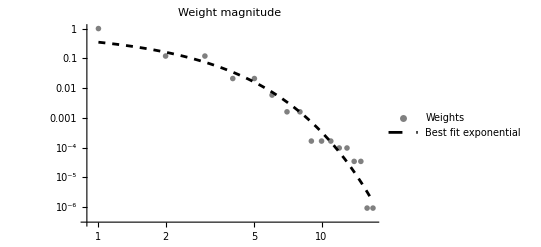

```mathematica
data=ReverseSort[Abs[Values[weights]]];
fit=Exp[LinearModelFit[Log[data[[;;-2]]],x,x]//Normal]//Simplify
Show[
ListLogLogPlot[data,
PlotMarkers->"OpenMarkers",
PlotStyle->Gray,
PlotLegends->{"Weights"}],
LogLogPlot[fit,{x,1,17},
PlotStyle->Directive[Dashed,Black],
PlotLegends->{"Best fit exponential"}],
PlotLabel->"Weight magnitude"]
```